## script

```mathematica
<<"C:\\Users\\aliha\\Desktop\\curvatureMeasure.m";
```

```mathematica
img=-Graphics-;
```

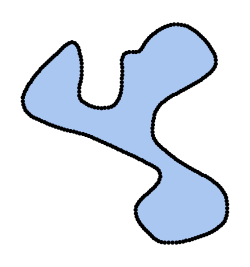

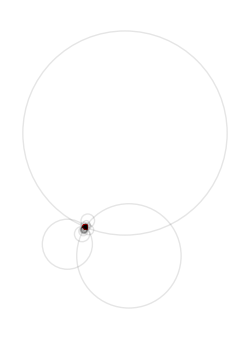

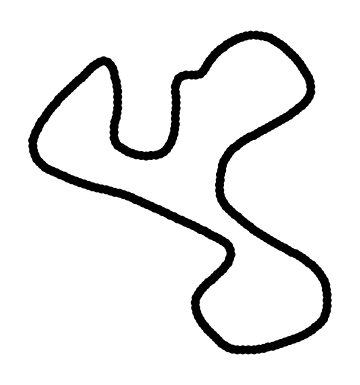

{0.0130321,0.0130414,0.0130044,0.0128871,0.0127183,0.0125187,0.0122205,0.0118521,0.011491,0.0108562,0.0101892,0.00946622,0.00861621,0.00786645,0.0068942,0.00601146,0.00515826,0.00426401,0.00341107,0.00269803,0.00230636,0.00158021,0.00086279,0.000424519,0.0000282316,-0.000376529,-0.000633437,-0.000784886,-0.000922318,-0.000902403,-0.00095165,-0.000964304,-0.000992369,-0.001102,-0.00118875,-0.00153581,-0.00191172,-0.00246727,-0.00293654,-0.0036961,-0.00428368,-0.00519656,-0.00604238,-0.0070812,-0.00814229,-0.00920884,-0.010119,-0.0110647,-0.0117371,-0.0122349,-0.0125807,-0.0126123,-0.0124547,-0.0123053,-0.0121813,-0.012009,-0.0118215,-0.0114447,-0.0109694,-0.010084,-0.00908037,-0.00755712,-0.00581586,-0.00380038,0.00148529,0.00102621,0.00341426,0.00588462,0.00801411,0.00964847,0.0108483,0.0116689,0.0122067,0.0126787,0.0129788,0.0133933,0.0138255,0.0140538,0.0142005,0.01409,0.0139582,0.0137144,0.013367,0.0130664,0.0127009,0.0122813,0.0118309,0.0113835,0.0108914,0.0105616,0.010249,0.0100619,0.010039,0.0100003,0.0101226,0.0102101,0.0103573,0.0106366,0.0108541,0.0111463,0.0114393,0.0116489,0.0118956,0.0119849,0.0121544,0.0122799,0.012437,0.0127216,0.0129326,0.0130916,0.0132161,0.0132871,0.0132949,0.013284,0.0131243,0.012969,0.0127459,0.0124352,0.0120315,0.0114774,0.0108674,0.0102088,0.00939212,0.0086058,0.00782405,0.00698429,0.00607296,0.00504553,0.00413912,0.00332794,0.00229913,0.00124136,0.000115213,-0.00103862,-0.00203465,-0.00306064,-0.0039274,-0.00472127,-0.00555757,-0.00621402,-0.00697097,-0.00768762,-0.00842497,-0.00903747,-0.00974315,-0.0103096,-0.0108119,-0.0112733,-0.0115861,-0.011832,-0.0120001,-0.0120937,-0.0121318,-0.0121117,-0.0120682,-0.0119525,-0.0118098,-0.0115963,-0.0112433,-0.0109754,-0.0104975,-0.0100271,-0.00931847,-0.00866909,-0.00774604,-0.00672885,-0.00545774,-0.00398683,-0.00274563,-0.00146937,-0.0000552569,0.00132449,0.00275596,0.00414363,0.0056044,0.00692662,0.00825334,0.00936144,0.0101554,0.0109852,0.0116521,0.0121922,0.0125307,0.0129397,0.0132717,0.0135139,0.0137778,0.0140094,0.014329,0.0146266,0.0148657,0.0150664,0.0151617,0.0152993,0.0152129,0.0151364,0.0149592,0.0147657,0.0145661,0.0142782,0.0140378,0.0136233,0.0131615,0.0124486,0.0117641,0.0109823,0.0104441,0.0100296,0.00986509,0.00979601,0.00984929,0.00989337,0.00982927,0.00968365,0.00945923,0.00926904,0.00902149,0.00857824,0.0081376,0.00756486,0.0069816,0.0063501,0.00586978,0.00580928,0.00577652,0.005849,0.00558655,0.00524047,0.00446665,0.00354405,0.00215248,0.000594322,-0.0010956,-0.00278641,-0.00435075,-0.00620945,-0.00811025,-0.00993161,-0.0116003,-0.0128778,-0.0139445,-0.0147499,-0.0153322,-0.0156752,-0.0157454,-0.0158676,-0.0160052,-0.0160334,-0.0161065,-0.0160104,-0.0158334,-0.0155119,-0.0152824,-0.0149948,-0.0149092,-0.0146983,-0.014105,-0.0130723,-0.0112107,-0.00870489,-0.00549171,-0.00181597,-0.00197501,-0.00559485,0.00869481,0.0110922,0.0127223,0.0136619,0.0142422,0.014588,0.0146235,0.0146321,0.014649,0.0147925,0.0152303,0.015683,0.0161371,0.0165097,0.016671,0.0165811,0.0161741,0.0160757,0.0153093,0.0144412,0.0134454,0.0123436,0.0116102,0.0109634,0.0105593,0.010068,0.0100337,0.0100876,0.0101365,0.0104036,0.0108286,0.0114294,0.0118991,0.0122862,0.0126517,0.0128776,0.0130081}

```mathematica
Quiet@curvatureMeasure[img,300,20]
```

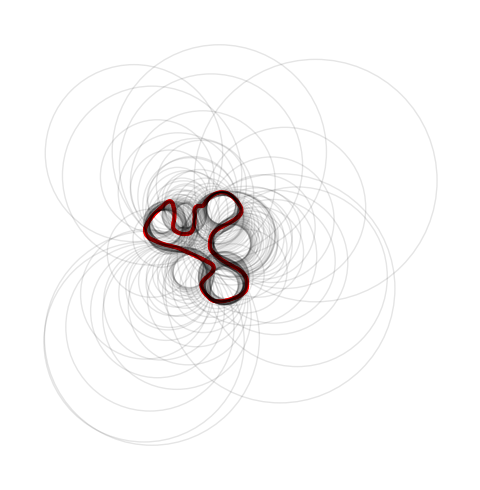

```mathematica
DeleteCases[Unevaluated[-Graphics-],Circle[_,x_/;x>500],{0,∞}]
```

```mathematica
img=-Graphics-;
```

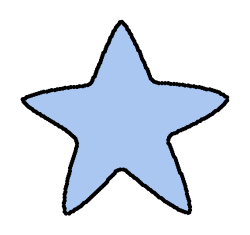

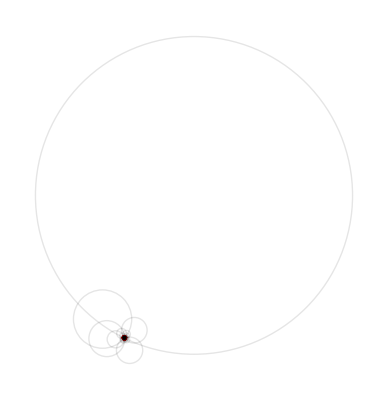

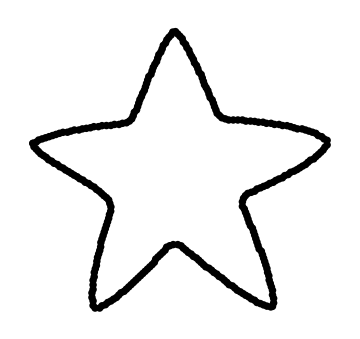

{0.0293148,0.0301219,0.0308889,0.0314711,0.0316841,0.0317731,0.0316383,0.0306239,0.0295039,0.02758,0.0233335,0.019339,0.0138891,0.00925902,0.00437842,-0.000349857,-0.00307851,-0.00614472,-0.00841266,-0.0106711,-0.0113362,-0.0133244,-0.0140104,-0.015139,-0.0158394,-0.0165237,-0.0168089,-0.0171011,-0.0173831,-0.0176444,-0.0171009,-0.0170986,-0.0161703,-0.0152145,-0.0144309,-0.0132321,-0.0118934,-0.0104448,-0.00892514,-0.00664485,-0.00503828,-0.00238398,-0.000524133,0.0024919,0.00562165,0.00929532,0.0129105,0.0167447,0.0203831,0.0235061,0.0259367,0.0274862,0.028488,0.0286288,0.0288255,0.0285826,0.0286801,0.0282176,0.0283953,0.0293891,0.0305686,0.0312988,0.0324056,0.0326669,0.0326264,0.0322256,0.0316213,0.0306744,0.0283769,0.0252029,0.0208605,0.0164836,0.0117876,0.0071009,0.0033874,-0.00034016,-0.00357598,-0.00628259,-0.00880366,-0.0113376,-0.0129304,-0.014963,-0.0164241,-0.0178026,-0.0189652,-0.0198012,-0.0205477,-0.0209861,-0.0215476,-0.0217234,-0.0217983,-0.0213382,-0.0209038,-0.0204201,-0.0194954,-0.0186517,-0.0174315,-0.0162915,-0.0149018,-0.0131049,-0.011565,-0.00946168,-0.0078005,-0.00606477,-0.00406126,-0.00260146,0.0000281994,0.00247393,0.00517096,0.00868347,0.0124532,0.0153343,0.0189036,0.0228102,0.0259719,0.028712,0.030503,0.03182,0.0323429,0.0325178,0.0323434,0.0323239,0.0319078,0.0310628,0.029952,0.0294092,0.0294545,0.029946,0.0303,0.0304888,0.0301993,0.0298988,0.0289599,0.0272099,0.0252102,0.0217577,0.0180517,0.0142787,0.0106823,0.00706685,0.00392154,0.000249137,-0.00257303,-0.00503511,-0.00745535,-0.00910905,-0.0111887,-0.0128203,-0.014468,-0.0162804,-0.0170627,-0.0181414,-0.0187262,-0.0197637,-0.0202682,-0.0206596,-0.0207338,-0.020721,-0.0204659,-0.0199279,-0.0193934,-0.0183258,-0.0172063,-0.0159798,-0.0144331,-0.0128608,-0.0108343,-0.00844071,-0.00570093,-0.00236818,-0.00015352,0.00407314,0.00720405,0.0117445,0.0156188,0.0196271,0.0236684,0.0262755,0.0280671,0.0292912,0.0302396,0.0306538,0.0308983,0.0306786,0.0302948,0.0297397,0.0287679,0.0282584,0.0283799,0.0279902,0.0280738,0.0273852,0.0270248,0.026209,0.0252792,0.023955,0.0218336,0.0192152,0.0164449,0.0133836,0.0094463,0.00675133,0.00369288,-0.00153025,-0.00117321,-0.00269023,-0.00462065,-0.00645495,-0.00776095,-0.00933765,-0.00973362,-0.0111569,-0.0122288,-0.0130311,-0.0135933,-0.0139914,-0.013893,-0.0140194,-0.0135567,-0.0132167,-0.0123558,-0.0119249,-0.0113387,-0.010453,-0.00916759,-0.00812753,-0.00658857,-0.00445183,-0.00171665,-0.00168823,0.00388205,0.00838316,0.0130241,0.0167733,0.0211653,0.0246103,0.0267204,0.0283037,0.0294289,0.0300279,0.0301532,0.0301075,0.0300883,0.0298125,0.0293006,0.0293512,0.0299123,0.0300337,0.0299894,0.0298337,0.0295703,0.0287823,0.0275172,0.0261032,0.0232417,0.0198061,0.0160651,0.0120276,0.0076537,0.00389487,-0.00143213,-0.00170343,-0.00405004,-0.006387,-0.00795178,-0.00909972,-0.0100515,-0.0107518,-0.0118395,-0.0124122,-0.0131264,-0.0132804,-0.013716,-0.0141073,-0.0139962,-0.0136796,-0.0130885,-0.0126128,-0.0115032,-0.0105897,-0.00968671,-0.00865608,-0.00716565,-0.0049733,-0.00322934,-0.000907777,-0.00197903,0.0047262,0.00926095,0.0131859,0.0170839,0.0216325,0.0242972,0.026351,0.0272625,0.0277984,0.0281635,0.0282616,0.0285097,0.0287009,0.0286932}

```mathematica
Quiet@curvatureMeasure[img,300,20]
```

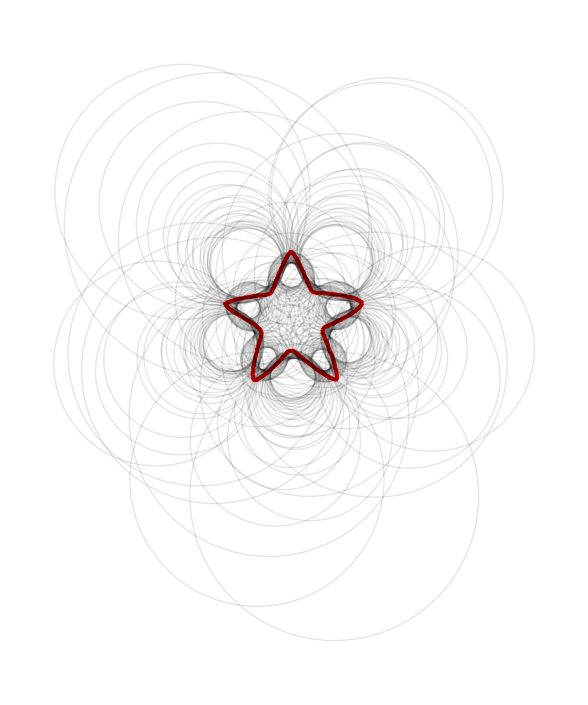

```mathematica
DeleteCases[Unevaluated[-Graphics-],Circle[_,x_/;x>300],{0,∞}]
```